# Stellations

C. Goodman-Strauss
(c) 1997, 1999

This notebook is designed to help create stellations of arbitrary polyhedra.  At the moment, only the creation of stellation grids is implemented.  Eventually, it would be nice to have all the main line stellations of a given polyhedron automatically generated.

### Preliminaries

We define homogeneous coordinates:

```mathematica
Homog[a_,b_,c_,d_]/;(d!=0)&&(d!=1):=Homog[a/d,b/d,c/d,1]
```

```mathematica
Homog[b_,c_,d_]/;(d!=0)&&(d!=1):=Homog[b/d,c/d,1]
```

## Stellation Patterns

A plane is given in four-dimensional homogeneous coordinates:  Homog[a,b,c,d].  It is assumed that d≠0 (that the plane does not pass through the origin).   The equation of the plane is thus  ax+by+cz+d==0; the normal is {a,b,c} and the point closest to the origin is {a,b,c}-d/(a^2+b^2+c^2). Distance to the origin is thus  d/(√(a^2+b^2+c^2))

We take some advantage of the (presumed) symmetry, and express the polyhedron in the following format 
 PolyPlanes[{Homog[...],....,Homog[...]},
 		...,
		{Homog[...],....,Homog[...]}]

where each list of homogeneous coordinates is one family of planes.

The routine is fairly simple.  After various calculations, which are detailed in the Work section below, we find formulas for expressing the line of intersection between planes {a,b,c,1} and [e,f,g,1}, written in homogeneous coordinates with  basis  {-b,a,0,1}, {-ac,-ab,a^2+b^2,1 (Several cases emerge; the general case is  af-be!=0)

The line {A,B,1} has equation Ax+By+1=0.  We use the routine DrawLine to create Line objects.

```mathematica
IntLine[v0_Homog,p_Homog]/;(Length[v0]==4 &&Length[p]==4):=Module[{a,b,c,e,f,g},
		{a,b,c}=Drop[List@@ v0,-1]/v0⟦-1⟧;
		{e,f,g}=Drop[List @@ p,-1]/p⟦-1⟧;
	 Which[
			(a==0)&&(b==0) (*plane is horizontal*),Homog[e,f,1-g/c],
			 Chop[a f - b e,10^-5]==0 (*planes are possibly parallel*),If[Chop[b g -c f,10^-5]===0,XXXX,Homog[0,-(-a c e-b c f+a^2 g+b^2 g)/(√(a^2+b^2)),-((-a c e-b c f+a^2 g+b^2 g) (a^2 b+b^3+b c^2-a^2 f-b^2 f-b c g))/((a^2+b^2) √(a^2+b^2+c^2)  (c f-b g))]],
			True (*general position*),Homog[(√(a^2+b^2+c^2) (b e-a f))/(√(a^2+b^2)),-(-a c e-b c f+a^2 g+b^2 g)/(√(a^2+b^2)),(a^2+b^2+c^2-a e-b f-c g)/(√(a^2+b^2+c^2))]]//Chop[#,10^-5]&]
```

```mathematica
StellationPatterns[poly_PolyPlanes]:=
	Table[ HLines @@ Map[IntLine[poly[[k,1]],#]&,Delete[poly,{k,1}],{2}],{k,1,Length[poly]}]
```

```mathematica
DrawLine[Homog[0,0,c_],R_]:=Null;
DrawLine[XXXX,R_]:=Null;
DrawLine[Homog[a_,b_,c_],R_]:=
	Module[{p,v},
		v={-b,a}/√(a^2+b^2);
		p=-c {a,b}/(a^2+b^2);
		Line[{p+1.41 R v,p-1.41 R v}]]
```

```mathematica
DrawStelLines[lines_HLines,R_,colorlist_,opts___]:=
	Show[Graphics[Select[Join @@ Join @@ Table[{{colorlist[[k]]},DrawLine[#,R]&/@ lines[[k]]},{k,1,Length[lines]}],(!(#===Null))&],opts,Axes->False,PlotRange->{{-R,R},{-R,R}},AspectRatio->Automatic]]
```

```mathematica
ncols[n_]:=ncols[n]=Table[Hue[k/n],{k,1,n}];
```

## Particular Examples

The original data was generated by one of the poly.nb packages written by C. Goodman-Strauss

### Small Rhombic Cuboctahedron

```mathematica
β=-1+√2//N;
```

```mathematica
smRhoCO=PolyPlanes[{Homog[0,0,-1,1],Homog[-1,0,0,1],Homog[0,-1,0,1],Homog[0,0,1,1],Homog[1,0,0,1],Homog[0,1,0,1]},{Homog[1,1,0,-1-β],Homog[0,1,1,-1-β],Homog[1,0,1,-1-β],Homog[1,-1,0,-1-β],Homog[0,1,-1,-1-β],Homog[-1,0,1,-1-β],Homog[-1,-1,0,-1-β],Homog[0,-1,-1,-1-β],Homog[-1,0,-1,-1-β],Homog[-1,1,0,-1-β],Homog[0,-1,1,-1-β],Homog[1,0,-1,-1-β]},{Homog[1,1,1,-1-2 β],Homog[1,-1,1,-1-2 β],Homog[-1,-1,1,-1-2 β],Homog[-1,1,1,-1-2 β],Homog[1,-1,-1,-1-2 β],Homog[-1,-1,-1,-1-2 β],Homog[-1,1,-1,-1-2 β],Homog[1,1,-1,-1-2 β]}]//Simplify;
```

```mathematica
smRhoCOStel=StellationPatterns[smRhoCO];
```

```mathematica
DrawStelLines[#,5,ncols[3]]& /@ smRhoCOStel
```

{⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃}

### The Snub Cube

#### hide this:

```mathematica
SnubCubePlanes=PolyPlanes[{Homog[0,0,-1,1],Homog[-1,0,0,1],Homog[0,-1,0,1],Homog[0,0,1,1],Homog[1,0,0,1],Homog[0,1,0,1]},{Homog[-0.543689012692076367,-0.543689012692076367,-0.543689012692076367,1],Homog[-0.543689012692076367,0.543689012692076367,-0.543689012692076367,1],Homog[0.543689012692076367,0.543689012692076367,-0.543689012692076367,1],Homog[0.543689012692076367,-0.543689012692076367,-0.543689012692076367,1],Homog[-0.543689012692076367,0.543689012692076367,0.543689012692076367,1],Homog[0.543689012692076367,0.543689012692076367,0.543689012692076367,1],Homog[0.543689012692076367,-0.543689012692076367,0.543689012692076367,1],Homog[-0.543689012692076367,-0.543689012692076367,0.543689012692076367,1]},{Homog[-0.543689012692076278,0.160713244785838842,-0.751908729830008315,1],Homog[-0.751908729830008581,-0.543689012692076367,0.16071324478583886,1],Homog[0.16071324478583886,-0.751908729830008581,-0.543689012692076367,1],Homog[-0.543689012692076278,-0.160713244785838842,0.751908729830008315,1],Homog[0.751908729830008581,-0.543689012692076367,-0.16071324478583886,1],Homog[-0.16071324478583886,0.751908729830008581,-0.543689012692076367,1],Homog[0.160713244785838842,0.543689012692076278,-0.751908729830008315,1],Homog[-0.751908729830008581,0.16071324478583886,0.543689012692076367,1],Homog[0.543689012692076367,-0.751908729830008581,0.16071324478583886,1],Homog[0.160713244785838842,-0.543689012692076278,0.751908729830008315,1],Homog[0.751908729830008581,0.16071324478583886,-0.543689012692076367,1],Homog[-0.543689012692076367,0.751908729830008581,0.16071324478583886,1],Homog[0.543689012692076278,-0.160713244785838842,-0.751908729830008315,1],Homog[-0.751908729830008581,0.543689012692076367,-0.16071324478583886,1],Homog[-0.16071324478583886,-0.751908729830008581,0.543689012692076367,1],Homog[0.543689012692076278,0.160713244785838842,0.751908729830008315,1],Homog[0.751908729830008581,0.543689012692076367,0.16071324478583886,1],Homog[0.16071324478583886,0.751908729830008581,0.543689012692076367,1],Homog[-0.160713244785838842,-0.543689012692076278,-0.751908729830008315,1],Homog[-0.751908729830008581,-0.16071324478583886,-0.543689012692076367,1],Homog[-0.543689012692076367,-0.751908729830008581,-0.16071324478583886,1],Homog[-0.160713244785838842,0.543689012692076278,0.751908729830008315,1],Homog[0.751908729830008581,-0.16071324478583886,0.543689012692076367,1],Homog[0.543689012692076367,0.751908729830008581,-0.16071324478583886,1]}];
```

#### ok

```mathematica
SnubCubeStel=StellationPatterns[SnubCubePlanes];
```

```mathematica
DrawStelLines[#,5,ncols[3]]& /@ SnubCubeStel
```

{⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃}

## Work

Only look at this part to see ugliness!

Finding the equations governing intersecting planes.

```mathematica
P1={a,b,c,1}
```

{a,b,c,1}

```mathematica
P2={e,f,g,1}
```

{e,f,g,1}

Og is our base point on the plane {a,b,c}; it is the point closest to the origin.

```mathematica
Og=-{a,b,c}/{a,b,c}.{a,b,c}
```

{-a/(a^2+b^2+c^2),-b/(a^2+b^2+c^2),-c/(a^2+b^2+c^2)}

X and Y are our chosen basis vectors in the plane {a,b,c}

```mathematica
X={-b,a,0}/√(a^2+b^2);
		
Y={-a c,-b c,a^2+b^2}/√((a^2+b^2+c^2)(a^2+b^2))
```

{-(a c)/(√((a^2+b^2) (a^2+b^2+c^2))),-(b c)/(√((a^2+b^2) (a^2+b^2+c^2))),(a^2+b^2)/(√((a^2+b^2) (a^2+b^2+c^2)))}

### Case 1

Assume   -b e+a f  != 0

Since  -b e+a f  != 0 we may set z=-1

```mathematica
z0=-1;
```

```mathematica
{x0,y0}=({x,y}/.(Solve[{P1.{x,y,-1,1}==0,P2.{x,y,-1,1}==0},{x,y}][[1]]))
```

{-(-b+f-c f+b g)/(-b e+a f),-(-a+e-c e+a g)/(b e-a f)}

p0 is a (more or less arbitrary) point on the line of intersection of the two planes.

```mathematica
p0={x0,y0,z0,1}
```

{-(-b+f-c f+b g)/(-b e+a f),-(-a+e-c e+a g)/(b e-a f),-1,1}

We now wish to express p0 in terms of X & Y; that is, we find A0, B0 with p0=A0 X + B0 Y+Og

```mathematica
{A0,B0}=({A,B}/.(Solve[{x0,y0,z0}==Og+A X+B Y,{A,B}]//Simplify)[[1]])//Expand//Simplify
```

{(a (e-c e)+b (f-c f+b (-1+g))+a^2 (-1+g))/(√(a^2+b^2) (-b e+a f)),-(a^2+b^2+(-1+c) c)/(√((a^2+b^2) (a^2+b^2+c^2)))}

Similarly, we find Av, Bv so that the direction of the line of intersection, {a,b,c}×{e,f,g}==Av X + Bv Y

```mathematica
{Av,Bv}=({A,B}/.
				(Solve[{a,b,c}×{e,f,g}==A X + B Y,{A,B}]//Simplify)[[1]])
```

{(a c e-a^2 g+b (c f-b g))/(√(a^2+b^2)),(√((a^2+b^2) (a^2+b^2+c^2)) (-b e+a f))/(a^2+b^2)}

And so now the equation we've been waiting for:
Shifting to coordinates in the plane, we now have as a basis X,Y; origin is Og; direction of the line is {Av,Bv} & the line passes through {A0,B0};  Hence the equation of the line is -Bv X + Av Y + Av B0 - A0 Bv ==0;
Hence the homogeneous coordinates are {-Bv, Av, Av B0 - A0 Bv}; the point closest to the origin is {Bv,-Av}(AB0-BA0)/(A^2+B^2)

```mathematica
{-Bv, Av, Av B0 - A0 Bv}//Simplify//Expand//Factor
```

{(√((a^2+b^2) (a^2+b^2+c^2)) (b e-a f))/(a^2+b^2),-(-a c e-b c f+a^2 g+b^2 g)/(√(a^2+b^2)),(√((a^2+b^2) (a^2+b^2+c^2)) (a^2+b^2+c^2-a e-b f-c g))/(√(a^2+b^2) (a^2+b^2+c^2))}

```mathematica
{(√(a^2+b^2+c^2) (b e-a f))/(√(a^2+b^2)),-(-a c e-b c f+a^2 g+b^2 g)/(√(a^2+b^2)),(a^2+b^2+c^2-a e-b f-c g)/(√(a^2+b^2+c^2))}
```

### Case 2

On the other hand, if   -b e+a f  == 0

If a/e=b/f=c/g, then the rank is all messed up and there is no point in proceeding.  So assume c/g!=a/e=b/f

For the moment, assume a!=0

We may set x=1 (since ag!=ec)

```mathematica
x0=-1;
```

```mathematica
{y0,z0}=
	({y,z}/.(Solve[{P1.{-1,y,z,1}==0,P2.{-1,y,z,1}==0},{y,z}][[1]]))
```

{-(-c+c e+g-a g)/(-c f+b g),-(b-b e-f+a f)/(-c f+b g)}

p0 is a (more or less arbitrary) point on the line of intersection of the two planes.

```mathematica
p0={x0,y0,z0,1}
```

{-1,-(-c+c e+g-a g)/(-c f+b g),-(b-b e-f+a f)/(-c f+b g),1}

We now wish to express p0 in terms of X & Y; that is, we find A0, B0 with p0=A0 X + B0 Y+Og

```mathematica
{A0,B0}=({A,B}/.(Solve[{x0,y0,z0}==Og+A X+B Y,{A,B}]//Simplify)[[1]])//Expand//Simplify
```

{(a^2 g-a (c (-1+e)+g)+b (-c f+b g))/(√(a^2+b^2) (-c f+b g)),(-a^3 f-a (b^2+c^2) f+a^2 (b (-1+e)+f)+b (b^2 (-1+e)+b f+c (c (-1+e)+g)))/(√((a^2+b^2) (a^2+b^2+c^2)) (-c f+b g))}

```mathematica
B0=(-a^2 b-b^3-b c^2+a^2 f+b^2 f+b c g)/ (√((a^2+b^2) (a^2+b^2+c^2)) (-c f+b g)) ;
```

Similarly, we find Av, Bv so that the direction of the line of intersection, {a,b,c}×{e,f,g}==Av X + Bv Y

```mathematica
{Av,Bv}=({A,B}/.
				(Solve[{a,b,c}×{e,f,g}==A X + B Y,{A,B}]//Simplify)[[1]])
```

{(a c e-a^2 g+b (c f-b g))/(√(a^2+b^2)),(√((a^2+b^2) (a^2+b^2+c^2)) (-b e+a f))/(a^2+b^2)}

```mathematica
{Av,Bv}={(a c e-a^2 g+b (c f-b g))/(√(a^2+b^2)),0} (*note -b e+a f=0*)
```

{(a c e-a^2 g+b (c f-b g))/(√(a^2+b^2)),0}

Just for example, here is a parametrization of the line; but we will take something slightly more useful.

```mathematica
ppp=Append[t(Av X+Bv Y)+A0 X+B0 Y+Og,1]//Simplify
```

{(b (-a c e+a^2 g+b (-c f+b g)) (-1-c f t+b g t))/((a^2+b^2) (-c f+b g)),(b^2 (c-g)+a^3 g (1+c f t-b g t)-a b (c f-b g) (1+c f t-b g t)-a^2 (g+c^2 e f t+c (-1+e-b e g t)))/((a^2+b^2) (-c f+b g)),(-b+f)/(-c f+b g),1}

```mathematica
ppp.P1//Simplify
```

0

```mathematica
ppp.P2//Simplify
```

((b e-a f) (-a c e+a^2 g+b (-c f+b g)) (-1-c f t+b g t))/((a^2+b^2) (-c f+b g))

And so now the equation we've been waiting for:
Shifting to coordinates in the plane, we now have as a basis X,Y; origin is Og; direction of the line is {Av,Bv} & the line passes through {A0,B0};  Hence the equation of the line is -Bv X + Av Y + Av B0 - A0 Bv ==0;
Hence the homogeneous coordinates are {-Bv, Av, Av B0 - A0 Bv}; the point closest to the origin is {Bv,-Av}(AB0-BA0)/(A^2+B^2)

```mathematica
{-Bv, Av, Av B0 - A0 Bv}//Simplify//Expand//Factor
```

{0,-(-a c e-b c f+a^2 g+b^2 g)/(√(a^2+b^2)),-(√((a^2+b^2) (a^2+b^2+c^2)) (-a c e-b c f+a^2 g+b^2 g) (a^2 b+b^3+b c^2-a^2 f-b^2 f-b c g))/((a^2+b^2)^(3/2) (a^2+b^2+c^2) (c f-b g))}

```mathematica
{0,-(-a c e-b c f+a^2 g+b^2 g)/(√(a^2+b^2)),-((-a c e-b c f+a^2 g+b^2 g) (a^2 b+b^3+b c^2-a^2 f-b^2 f-b c g))/((a^2+b^2) √(a^2+b^2+c^2)  (c f-b g))}
```

Finding the coordinates of planes for various polyhedra

This particular part should be rewritten directly in terms of homogeneous coordinates.

## Polyhedral groups

These    are generators   for all the platonic symmetries

```mathematica
g=N /@ (Sqrt[5] +1)/2;  
t=1/g;
```

These    are generators   for all the platonic symmetries

```mathematica
Invert[dodont_Integer (*Mod 2*)][vect_List]:= 
		vect*{{1,1,1},{-1,-1,-1}}[[dodont]]
 
RAlong[axis_Integer(*x-1,z-3*)][dodont_Integer (*Mod 2*)][vect_List]:=
		vect*{{1,1,1},RotateRight[{-1,1,1},axis-1]}[[dodont]]


R5=Table[MatrixPower[.5{{1,-g,t},{g,t,-1},{t,1,g}},k],{k,0,4}];

Rot5[pinth_Integer (*Mod 5*)(*about   (1,0,g)*)][vect_List]:=
		Dot[R5[[pinth]],vect]

Rot3[pinth_Integer (*Mod 3*)(*cwise about   (1,1,1)*)][vect_List]:=
		RotateRight[vect,pinth-1]
				
Ident[vect_]:=vect

Tet[n_][vect_List]:=vect {{1,1,1},{1,-1,-1},{-1,1,-1},{-1,-1,1}}⟦n⟧
(* given a  face and a generator  mmap of order order, 
	fimages gives
a list of all the images of the face *)

fimages[mmap_,order_,face_]:=    Chop[#,10^-13]& @ 
	Table[
		mmap[k][face[[j]]],
			{k,1,order},{j,1,Length[face]}]
```

```mathematica
pair2homo[{p_,n_}]:=Homog@@ Append[n,-n.p]
```

## the Small Rhombic Cubocta:

### drawing the polyhedron

```mathematica
dd[x_,y_]:=(x-y).(x-y)
```

```mathematica
vertrhco= {a,a,1} /. (Solve[   dd[{a,a,1},{1,a,a}] == 
          dd[{a,a,1},{-a,a,1}],a] //N )[[2]]
```

{0.414214, 0.414214, 1}

```mathematica
SquareFace1 = Join @@ 
	(fimages[Rot4,4,{vertrhco}]);
```

```mathematica
SquareFaces1=  
		Join @@ (  fimages[Rot3,3,#]& /@ 
		fimages[InvertThrough[3],2,SquareFace1] );
```

```mathematica
TriFace =  Join @@ 
	(fimages[Rot3,3,{vertrhco}]);

TriFaces=  Join @@ (  fimages[Rot4,4,#]& /@ 
		fimages[InvertThrough[3],2,TriFace] );
```

```mathematica
SquareFace2 = Rot3[2] /@ {vertrhco, Rot4[2][vertrhco], 
                 Rot3[2][Rot4[4][vertrhco]], Rot3[2][vertrhco]}
```

{{1, 0.414214, 0.414214}, {1., 0.414214, -0.414214}, {0.414214, 1., -0.414214}, 
 
  {0.414214, 1, 0.414214}}

```mathematica
SquareFaces2= 
        Join @@ (  fimages[Rot3,3,#]& /@ 
		fimages[Rot4,4,SquareFace2] );
```

```mathematica
RhCo=  	Join @@ {{GrayLevel[.9]},
				 	Polygon /@ SquareFaces1, 
				 	{GrayLevel[.40]},
					Polygon /@TriFaces, 
					{GrayLevel[.60]},
					Polygon /@SquareFaces2};
```

```mathematica
Show[Graphics3D[RhCo] ,Lighting->False,Boxed->False]
```

-Graphics3D-

### getting the face planes

```mathematica
Clear[β]
```

```mathematica
SquarePlane1 = {{β,β,1},{0,0,1}};
SquarePlanes1=  
		Join @@ (  fimages[Rot3,3,#]& /@ 
		fimages[InvertThrough[3],2,SquarePlane1] );
TriPlane = {{β,β,1},{1,1,1}};

TriPlanes=  Join @@ (  fimages[Rot4,4,#]& /@ 
		fimages[InvertThrough[3],2,TriPlane] );
SquarePlane2 = Rot3[2] /@ {{β,β,1}, {1,0,1}};
SquarePlanes2= 
        Join @@ (  fimages[Rot3,3,#]& /@ 
		fimages[Rot4,4,SquarePlane2] );
```

```mathematica
Map[pair2homo,{SquarePlanes1,SquarePlanes2,TriPlanes},{2}]
```

{{Homog[0,0,-1,1],Homog[-1,0,0,1],Homog[0,-1,0,1],Homog[0,0,1,1],Homog[1,0,0,1],Homog[0,1,0,1]},{Homog[1,1,0,-1-β],Homog[0,1,1,-1-β],Homog[1,0,1,-1-β],Homog[1,-1,0,-1-β],Homog[0,1,-1,-1-β],Homog[-1,0,1,-1-β],Homog[-1,-1,0,-1-β],Homog[0,-1,-1,-1-β],Homog[-1,0,-1,-1-β],Homog[-1,1,0,-1-β],Homog[0,-1,1,-1-β],Homog[1,0,-1,-1-β]},{Homog[1,1,1,-1-2 β],Homog[1,-1,1,-1-2 β],Homog[-1,-1,1,-1-2 β],Homog[-1,1,1,-1-2 β],Homog[1,-1,-1,-1-2 β],Homog[-1,-1,-1,-1-2 β],Homog[-1,1,-1,-1-2 β],Homog[1,1,-1,-1-2 β]}}

## The Snub Cube

### drawing the polyhedron

```mathematica
dd[x_,y_]:=(x-y).(x-y)
```

```mathematica
vertsnub= {a,b,1} /. (Solve[{   dd[{a,b,1},{1,-b,a}] == 
          dd[{a,b,1},{-b,a,1}] ==
          dd[{a,b,1},{1,a,b}]  } ,{a,b}] //N )[[3]]
```

{0.543689,0.295598,1}

```mathematica
SquareFace = Join @@ 
	(fimages[Rot4,4,{vertsnub}])
```

{{0.543689,0.295598,1.},{0.295598,-0.543689,1.},{-0.543689,-0.295598,1.},{-0.295598,0.543689,1.}}

```mathematica
SquareFaces=  
		Join @@ (  fimages[Rot3,3,#]& /@ 
		fimages[InvertThrough[3],2,SquareFace] );
```

General::spell1: Possible spelling error: new symbol name "SquareFaces" is similar to existing symbol "SquareFace".

```mathematica
TriFace1 =  Join @@ 
	(fimages[Rot3,3,{vertsnub}]);

TriFaces1=  Join @@ (  fimages[Rot4,4,#]& /@ 
		fimages[InvertThrough[3],2,TriFace1] );
```

General::spell1: Possible spelling error: new symbol name "TriFaces1" is similar to existing symbol "TriFace1".

```mathematica
TriFace2 = {Rot4[2][vertsnub], Rot4[1][vertsnub], 
Rot3[2][Rot4[4][vertsnub]]}
TriFaces2= 
            
		Join @@ (  fimages[Rot3,3,#]& /@ (Join @@ 
		(fimages[InvertThrough[3],2,#]& /@
		fimages[Rot4,4,TriFace2] )));
```

{{0.295598,-0.543689,1.},{0.543689,0.295598,1.},{1.,-0.295598,0.543689}}

General::spell1: Possible spelling error: new symbol name "TriFaces2" is similar to existing symbol "TriFace2".

```mathematica
SnubCube=  	Join @@ {{GrayLevel[.9]},
				 	Polygon /@ SquareFaces, 
				 	{GrayLevel[.40]},
					Polygon /@TriFaces1, 
					{GrayLevel[.60]},
					Polygon /@TriFaces2};
```

```mathematica
Show[Graphics3D[SnubCube] ,Lighting->False,Boxed->False]
```

⁃Graphics3D⁃

### getting the face planes

```mathematica
SquarePlane= {{0,0,1},{0,0,1}};
SquarePlanes= Join @@ (  fimages[Rot3,3,#]& /@ 
		fimages[InvertThrough[3],2,SquarePlane] );

TriPlane1 = { vertsnub,{1,1,1} };
TriPlanes1= Join @@ (  fimages[Rot4,4,#]& /@ 
		fimages[InvertThrough[3],2,TriPlane1] );
TriPlane2 = {vertsnub, Plus @@ TriFace2};
TriPlanes2= 
            
		Join @@ (  fimages[Rot3,3,#]& /@ (Join @@ 
		(fimages[InvertThrough[3],2,#]& /@
		fimages[Rot4,4,TriPlane2] )));

SnubPlanes = { SquarePlanes, TriPlanes1, TriPlanes2};
```

```mathematica
SnubCubePlanes=Map[pair2homo,SnubPlanes,{2}]
```

{{Homog[0,0,-1,1],Homog[-1,0,0,1],Homog[0,-1,0,1],Homog[0,0,1,1],Homog[1,0,0,1],Homog[0,1,0,1]},{Homog[-0.543689,-0.543689,-0.543689,1],Homog[-0.543689,0.543689,-0.543689,1],Homog[0.543689,0.543689,-0.543689,1],Homog[0.543689,-0.543689,-0.543689,1],Homog[-0.543689,0.543689,0.543689,1],Homog[0.543689,0.543689,0.543689,1],Homog[0.543689,-0.543689,0.543689,1],Homog[-0.543689,-0.543689,0.543689,1]},{Homog[-0.543689,0.160713,-0.751909,1],Homog[-0.751909,-0.543689,0.160713,1],Homog[0.160713,-0.751909,-0.543689,1],Homog[-0.543689,-0.160713,0.751909,1],Homog[0.751909,-0.543689,-0.160713,1],Homog[-0.160713,0.751909,-0.543689,1],Homog[0.160713,0.543689,-0.751909,1],Homog[-0.751909,0.160713,0.543689,1],Homog[0.543689,-0.751909,0.160713,1],Homog[0.160713,-0.543689,0.751909,1],Homog[0.751909,0.160713,-0.543689,1],Homog[-0.543689,0.751909,0.160713,1],Homog[0.543689,-0.160713,-0.751909,1],Homog[-0.751909,0.543689,-0.160713,1],Homog[-0.160713,-0.751909,0.543689,1],Homog[0.543689,0.160713,0.751909,1],Homog[0.751909,0.543689,0.160713,1],Homog[0.160713,0.751909,0.543689,1],Homog[-0.160713,-0.543689,-0.751909,1],Homog[-0.751909,-0.160713,-0.543689,1],Homog[-0.543689,-0.751909,-0.160713,1],Homog[-0.160713,0.543689,0.751909,1],Homog[0.751909,-0.160713,0.543689,1],Homog[0.543689,0.751909,-0.160713,1]}}

## The Icosahedron

We should check that we really understand what's happening

```mathematica
icosaplane={{1,0,g},{1,1,1}}
```

{{1,0,1.61803},{1,1,1}}

```mathematica
icosaplanes={  
		Join @@ (  fimages[Rot5,5,#]& /@ 
		fimages[Tet,4,icosaplane] )}
```

{{{{1.,0,1.61803},{1.,1.,1.}},{{1.,0,1.61803},{0,0.618034,1.61803}},{{1.,0,1.61803},{0,-0.618034,1.61803}},{{1.,0,1.61803},{1.,-1.,1.}},{{1.,0,1.61803},{1.61803,0,0.618034}},{{1.,0,-1.61803},{1.,-1.,-1.}},{{0,1.61803,-1.},{1.,1.,-1.}},{{-1.61803,1.,0},{-0.618034,1.61803,0}},{{-1.61803,-1.,0},{-1.61803,0,0.618034}},{{0,-1.61803,-1.},{-0.618034,-1.61803,0}},{{-1.,0,-1.61803},{-1.,1.,-1.}},{{-1.,0,-1.61803},{-1.61803,0,-0.618034}},{{-1.,0,-1.61803},{-1.,-1.,-1.}},{{-1.,0,-1.61803},{0,-0.618034,-1.61803}},{{-1.,0,-1.61803},{0,0.618034,-1.61803}},{{-1.,0,1.61803},{-1.,-1.,1.}},{{0,-1.61803,1.},{0.618034,-1.61803,0}},{{1.61803,-1.,0},{1.61803,0,-0.618034}},{{1.61803,1.,0},{0.618034,1.61803,0}},{{0,1.61803,1.},{-1.,1.,1.}}}}

```mathematica
IcosaStelPlanes=PolyPlanes@@ Map[pair2homo,icosaplanes,{2}]
```

PolyPlanes[{Homog[-0.381966,-0.381966,-0.381966,1],Homog[0,-0.236068,-0.618034,1],Homog[0,0.236068,-0.618034,1],Homog[-0.381966,0.381966,-0.381966,1],Homog[-0.618034,0,-0.236068,1],Homog[-0.381966,0.381966,0.381966,1],Homog[-0.381966,-0.381966,0.381966,1],Homog[0.236068,-0.618034,0,1],Homog[0.618034,0,-0.236068,1],Homog[0.236068,0.618034,0,1],Homog[0.381966,-0.381966,0.381966,1],Homog[0.618034,0,0.236068,1],Homog[0.381966,0.381966,0.381966,1],Homog[0,0.236068,0.618034,1],Homog[0,-0.236068,0.618034,1],Homog[0.381966,0.381966,-0.381966,1],Homog[-0.236068,0.618034,0,1],Homog[-0.618034,0,0.236068,1],Homog[-0.236068,-0.618034,0,1],Homog[0.381966,-0.381966,-0.381966,1]}]

```mathematica
IcosaStel=StellationPatterns[IcosaStelPlanes];
```

```mathematica
DrawStelLines[#,10,{Hue[0]}]& /@ IcosaStel
```

{⁃Graphics⁃}

## the Great Rhombic Cubocta:

### drawing the polyhedron

```mathematica
dd[x_,y_]:=(x-y).(x-y)
```

```mathematica
(Solve[  {
			dd[{a,b,1},{1,b,a}] ==  dd[{a,b,1},{b,a,1}],
			dd[{a,b,1},{1,b,a}]==dd[{a,b,1},{a,-b,1}]},
		{a,b}] )
```

{{a→1-√2,b→1},{a→1+√2,b→1},{b→1/7 (-1-2 √2),a→1/7 (3-√2)},{b→1/7 (-1+2 √2),a→1/7 (3+√2)}}

Actually, the first 2 solutions give the truncated cube; the second two are the gr. rh. cubo.

```mathematica
{va,vb}= {a,b} /. 
	(Solve[  {
			dd[{a,b,1},{1,b,a}] ==  dd[{a,b,1},{b,a,1}],
			dd[{a,b,1},{1,b,a}]==dd[{a,b,1},{a,-b,1}]},
		{a,b}] )[[4]]
```

{1/7 (3+√2),1/7 (-1+2 √2)}

```mathematica
vertrhco={va,vb,1};
```

```mathematica
Octaface = Join @@ 
	(fimages[Rot4,4,{{vb,va,1},vertrhco}]);
```

```mathematica
Octafaces=  
		Join @@ (  fimages[Rot3,3,#]& /@ 
		fimages[InvertThrough[3],2,Octaface] );
```

```mathematica
Hexface =  Join @@ 
	(fimages[Rot3,3,{{vb,va,1},vertrhco}]);

Hexfaces=  Join @@ (  fimages[Rot4,4,#]& /@ 
		fimages[InvertThrough[3],2,Hexface] );
```

General::spell1: Possible spelling error: new symbol name "Hexface" is similar to existing symbol "Hexace".

General::spell1: Possible spelling error: new symbol name "Hexfaces" is similar to existing symbol "Hexface".

```mathematica
Squareface = Rot3[2] /@ {vertrhco, Rot4[2][vertrhco], 
                 Rot3[2][Rot4[4][vertrhco]], Rot3[2][vertrhco]}
```

General::spell1: Possible spelling error: new symbol name "Squareface" is similar to existing symbol "SquareFace".

{{1,1/7 (3+√2),1/7 (-1+2 √2)},{1,1/7 (-1+2 √2),1/7 (-3-√2)},{1/7 (3+√2),1,1/7 (1-2 √2)},{1/7 (-1+2 √2),1,1/7 (3+√2)}}

```mathematica
Squarefaces= 
        Join @@ (  fimages[Rot3,3,#]& /@ 
		fimages[Rot4,4,Squareface] );
```

```mathematica
RhCo=  	Join @@ {{GrayLevel[.9]},
				 	Polygon /@ Octafaces, 
				 	{GrayLevel[.40]},
					Polygon /@Hexfaces, 
					{GrayLevel[.60]},
					Polygon /@Squarefaces};
```

```mathematica
Show[Graphics3D[RhCo] ,Lighting->False,Boxed->False]
```

⁃Graphics3D⁃

### getting the face planes

```mathematica
OctaPlane = {vertrhco,{0,0,1}};
OctaPlanes=  
		Join @@ (  fimages[Rot3,3,#]& /@ 
		fimages[InvertThrough[3],2,OctaPlane] );
HexPlane = {vertrhco,{1,1,1}};

HexPlanes=  Join @@ (  fimages[Rot4,4,#]& /@ 
		fimages[InvertThrough[3],2,HexPlane] );
SquarePlane = Rot3[2] /@ {vertrhco, {1,0,1}};
SquarePlanes= 
        Join @@ (  fimages[Rot3,3,#]& /@ 
		fimages[Rot4,4,SquarePlane] );
```

General::spell1: Possible spelling error: new symbol name "OctaPlanes" is similar to existing symbol "OctaPlane".

General::spell1: Possible spelling error: new symbol name "HexPlanes" is similar to existing symbol "HexPlane".

```mathematica
grco=PolyPlanes@@ Map[pair2homo,{OctaPlanes,HexPlanes,SquarePlanes},{2}]//N;
```

```mathematica
grcoStel=StellationPatterns[grco];
```

```mathematica
DrawStelLines[#,6,ncols[3]]& /@ grcoStel
```

{⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃}

## the Rhombic Triacontahedron:

```mathematica
rhTriPlane={{0,0,1},{0,0,1}}
```

{{0,0,1},{0,0,1}}

```mathematica
rhTriPlanes={  Join @@ (  fimages[Rot5,5,#]& /@ 
		(Join @@ (  fimages[Rot3,3,#]& /@ 
		fimages[RAlong[3],2,rhTriPlane] )))}
```

{{{{0,0,1.},{0,0,1.}},{{0.309017,-0.5,0.809017},{0.309017,-0.5,0.809017}},{{0.809017,-0.309017,0.5},{0.809017,-0.309017,0.5}},{{0.809017,0.309017,0.5},{0.809017,0.309017,0.5}},{{0.309017,0.5,0.809017},{0.309017,0.5,0.809017}},{{1.,0,0},{1.,0,0}},{{0.5,0.809017,0.309017},{0.5,0.809017,0.309017}},{{-0.309017,0.5,0.809017},{-0.309017,0.5,0.809017}},{{-0.309017,-0.5,0.809017},{-0.309017,-0.5,0.809017}},{{0.5,-0.809017,0.309017},{0.5,-0.809017,0.309017}},{{0,1.,0},{0,1.,0}},{{-0.809017,0.309017,0.5},{-0.809017,0.309017,0.5}},{{-0.5,-0.809017,0.309017},{-0.5,-0.809017,0.309017}},{{0.5,-0.809017,-0.309017},{0.5,-0.809017,-0.309017}},{{0.809017,0.309017,-0.5},{0.809017,0.309017,-0.5}},{{0,0,-1.},{0,0,-1.}},{{-0.309017,0.5,-0.809017},{-0.309017,0.5,-0.809017}},{{-0.809017,0.309017,-0.5},{-0.809017,0.309017,-0.5}},{{-0.809017,-0.309017,-0.5},{-0.809017,-0.309017,-0.5}},{{-0.309017,-0.5,-0.809017},{-0.309017,-0.5,-0.809017}},{{-1.,0,0},{-1.,0,0}},{{-0.5,-0.809017,-0.309017},{-0.5,-0.809017,-0.309017}},{{0.309017,-0.5,-0.809017},{0.309017,-0.5,-0.809017}},{{0.309017,0.5,-0.809017},{0.309017,0.5,-0.809017}},{{-0.5,0.809017,-0.309017},{-0.5,0.809017,-0.309017}},{{0,-1.,0},{0,-1.,0}},{{0.809017,-0.309017,-0.5},{0.809017,-0.309017,-0.5}},{{0.5,0.809017,-0.309017},{0.5,0.809017,-0.309017}},{{-0.5,0.809017,0.309017},{-0.5,0.809017,0.309017}},{{-0.809017,-0.309017,0.5},{-0.809017,-0.309017,0.5}}}}

```mathematica
rhTriStelPlanes=PolyPlanes@@ Map[pair2homo,rhTriPlanes,{2}]
```

PolyPlanes[{Homog[0.,0.,-1.,1],Homog[-0.309017,0.5,-0.809017,1],Homog[-0.809017,0.309017,-0.5,1],Homog[-0.809017,-0.309017,-0.5,1],Homog[-0.309017,-0.5,-0.809017,1],Homog[-1.,0.,0.,1],Homog[-0.5,-0.809017,-0.309017,1],Homog[0.309017,-0.5,-0.809017,1],Homog[0.309017,0.5,-0.809017,1],Homog[-0.5,0.809017,-0.309017,1],Homog[0.,-1.,0.,1],Homog[0.809017,-0.309017,-0.5,1],Homog[0.5,0.809017,-0.309017,1],Homog[-0.5,0.809017,0.309017,1],Homog[-0.809017,-0.309017,0.5,1],Homog[0.,0.,1.,1],Homog[0.309017,-0.5,0.809017,1],Homog[0.809017,-0.309017,0.5,1],Homog[0.809017,0.309017,0.5,1],Homog[0.309017,0.5,0.809017,1],Homog[1.,0.,0.,1],Homog[0.5,0.809017,0.309017,1],Homog[-0.309017,0.5,0.809017,1],Homog[-0.309017,-0.5,0.809017,1],Homog[0.5,-0.809017,0.309017,1],Homog[0.,1.,0.,1],Homog[-0.809017,0.309017,0.5,1],Homog[-0.5,-0.809017,0.309017,1],Homog[0.5,-0.809017,-0.309017,1],Homog[0.809017,0.309017,-0.5,1]}]

```mathematica
rhTriStel=StellationPatterns[rhTriStelPlanes];
```

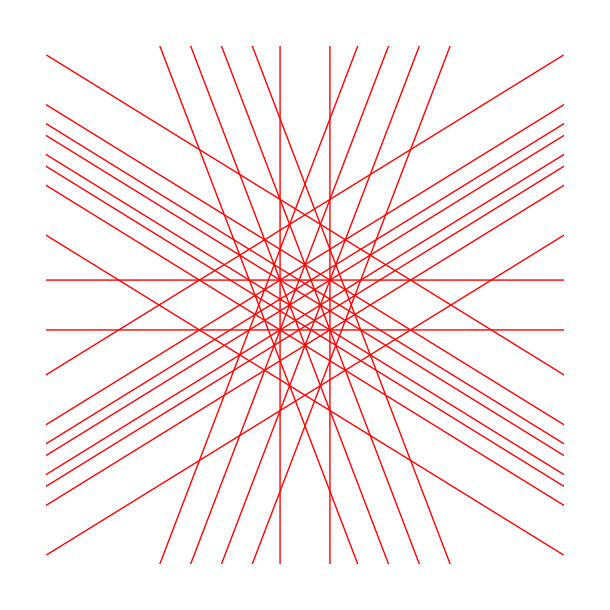

```mathematica
DrawStelLines[#,10,{Hue[0]}]& /@ rhTriStel
```

## the triakis octahedron

```mathematica
p={(1+Tan[π/8])/2 ,(1+Tan[π/8])/2,1};q={(1+Tan[π/8])/2,1,(1+Tan[π/8])/2};r={0,1,1};
```

```mathematica
n=((p-r)×(q-r))//N
```

{0.0857864,0.207107,0.207107}

```mathematica
triOPlane={r,n}
```

{{0,1,1},{0.0857864,0.207107,0.207107}}

```mathematica
triOPlanes={  Join @@ (  fimages[Tet,4,#]& /@ 
		(Join @@ (  fimages[RAlong[3],2,#]& /@ 
		fimages[Rot3,3,triOPlane] )))}
```

{{{{0,1,1},{0.0857864,0.207107,0.207107}},{{0,-1,-1},{0.0857864,-0.207107,-0.207107}},{{0,1,-1},{-0.0857864,0.207107,-0.207107}},{{0,-1,1},{-0.0857864,-0.207107,0.207107}},{{0,1,-1},{0.0857864,0.207107,-0.207107}},{{0,-1,1},{0.0857864,-0.207107,0.207107}},{{0,1,1},{-0.0857864,0.207107,0.207107}},{{0,-1,-1},{-0.0857864,-0.207107,-0.207107}},{{1,0,1},{0.207107,0.0857864,0.207107}},{{1,0,-1},{0.207107,-0.0857864,-0.207107}},{{-1,0,-1},{-0.207107,0.0857864,-0.207107}},{{-1,0,1},{-0.207107,-0.0857864,0.207107}},{{1,0,-1},{0.207107,0.0857864,-0.207107}},{{1,0,1},{0.207107,-0.0857864,0.207107}},{{-1,0,1},{-0.207107,0.0857864,0.207107}},{{-1,0,-1},{-0.207107,-0.0857864,-0.207107}},{{1,1,0},{0.207107,0.207107,0.0857864}},{{1,-1,0},{0.207107,-0.207107,-0.0857864}},{{-1,1,0},{-0.207107,0.207107,-0.0857864}},{{-1,-1,0},{-0.207107,-0.207107,0.0857864}},{{1,1,0},{0.207107,0.207107,-0.0857864}},{{1,-1,0},{0.207107,-0.207107,0.0857864}},{{-1,1,0},{-0.207107,0.207107,0.0857864}},{{-1,-1,0},{-0.207107,-0.207107,-0.0857864}}}}

```mathematica
triOStelPlanes=PolyPlanes@@ Map[pair2homo,triOPlanes,{2}]
```

PolyPlanes[{Homog[-0.207107,-0.5,-0.5,1],Homog[-0.207107,0.5,0.5,1],Homog[0.207107,-0.5,0.5,1],Homog[0.207107,0.5,-0.5,1],Homog[-0.207107,-0.5,0.5,1],Homog[-0.207107,0.5,-0.5,1],Homog[0.207107,-0.5,-0.5,1],Homog[0.207107,0.5,0.5,1],Homog[-0.5,-0.207107,-0.5,1],Homog[-0.5,0.207107,0.5,1],Homog[0.5,-0.207107,0.5,1],Homog[0.5,0.207107,-0.5,1],Homog[-0.5,-0.207107,0.5,1],Homog[-0.5,0.207107,-0.5,1],Homog[0.5,-0.207107,-0.5,1],Homog[0.5,0.207107,0.5,1],Homog[-0.5,-0.5,-0.207107,1],Homog[-0.5,0.5,0.207107,1],Homog[0.5,-0.5,0.207107,1],Homog[0.5,0.5,-0.207107,1],Homog[-0.5,-0.5,0.207107,1],Homog[-0.5,0.5,-0.207107,1],Homog[0.5,-0.5,-0.207107,1],Homog[0.5,0.5,0.207107,1]}]

```mathematica
triOStel=StellationPatterns[triOStelPlanes];
```

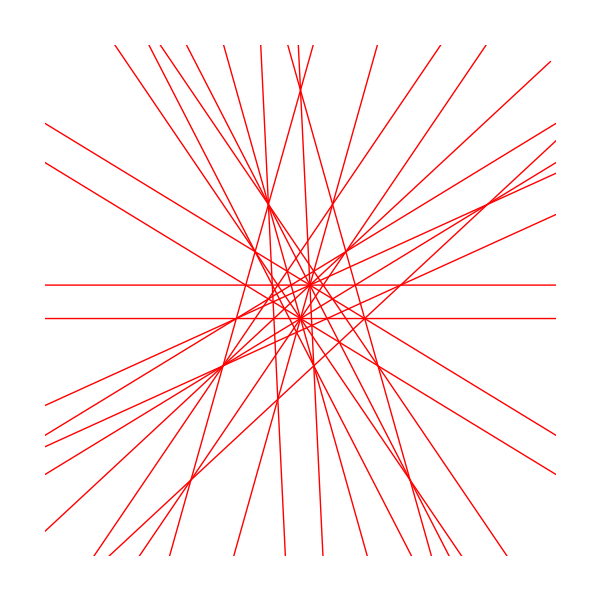

```mathematica
DrawStelLines[#,20,{Hue[0]}]& /@ triOStel
```

```mathematica
1/(1+2^.5)
```

0.414214